```mathematica
Llist[h_,L_] := Table [ - h/(2) ,2 L] 
 Ldown[h_,L_] := DiagonalMatrix[Llist[h,L],1]
Lup[h_,L_] := DiagonalMatrix[Llist[h,L],-1]
LzLz[h_,L_] := DiagonalMatrix[Table[m^2 /(2)+h,{m,-L, L }] ]
FluxPlaqOperator[g_,L_]  := LzLz[g,L]+  Ldown[g,L]+  Lup[g,L]
```

```mathematica
Clup[g_, L_]:=Lup[g,L]- g^2/(2)Table[If[i ==1&&j == 2L+1,1,0],{i,1,2L +1},{j,1,2 L+1}]
Cldown[g_, L_]:=Ldown[g,L]- g^2/(2)Table[If[i ==2L +1&&j == 1,1,0],{i,1,2L +1},{j,1,2 L+1}]
ClPlaqOperator[g_,L_]  := LzLz[g,L]+  Cldown[g,L]+  Clup[g,L]
```

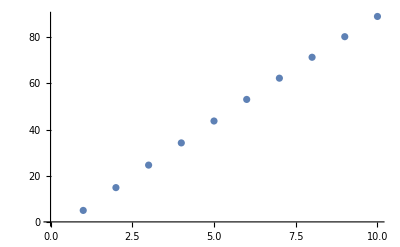

```mathematica
L=200; 
ListPlot[Sort[Eigenvalues[FluxPlaqOperator[10, L]//N], Less][[1;;10]]]
```

```mathematica
Psi[n_, x_, w_]:=(1/Sqrt[2^n n!])(w/Pi)^(1/4)Exp[-w x^2/2]HermiteH[n, Sqrt[w]x]
```

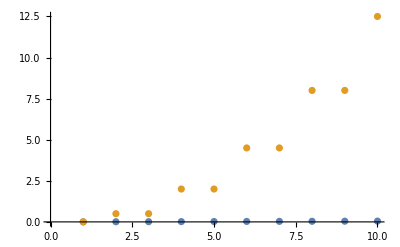

```mathematica
g = 0.01; 
ListPlot[{Table[g (i+1/2), {i, 0, 9}]+g ^2Table[Integrate[Psi[n, x, g] (Cos[x]-x^2/2) Psi[n, x, g], {x, -Infinity, Infinity}], {n, 0, 9}], Sort[Eigenvalues[FluxPlaqOperator[g, 400]//N], Less][[1;;10]]}]
```

```mathematica
Integrate[Psi[1, x, Sqrt[g]] (Cos[x]-x^2/2) Psi[1, x, Sqrt[g]], {x, -Infinity, Infinity}]//N
```

-0.3606

```mathematica
L=4;
U=DiagonalMatrix[Table [ 1,2L] ,1];
Udag=DiagonalMatrix[Table [ 1,2L] ,-1];
com=U.Udag-Udag.U;
comMat[g_]:=({evals, evecs}=Eigensystem[FluxPlaqOperator[h, L]];
evecs=(Normalize/@evecs[[Ordering[evals]]]);
Return[Table[evecs[[i]].com.evecs[[j]], {i, 1, 2L+1}, {j, 1, 2L+1}]];);
matlist=Table[comMat[h]//Abs, {h, 0.01, 5.0, 0.01}];
```

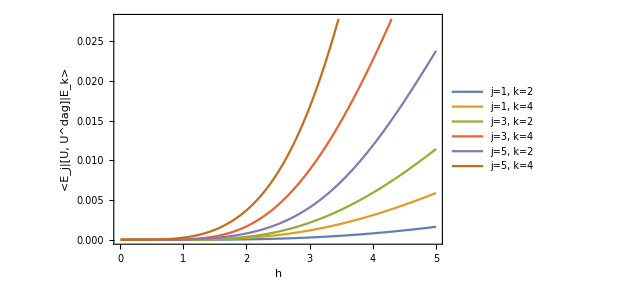

```mathematica
comElement[i_, j_]:=Transpose[{Table[h, {h, 0.01, 5.0, 0.01}], matlist[[All, i, j]]}]
ListPlot[{comElement[1, 2], comElement[1, 4], comElement[3, 2], comElement[3, 4], comElement[5, 2], comElement[5, 4]}, Joined->True, PlotLegends-> Placed[LineLegend[{"j=1, k=2", "j=1, k=4", "j=3, k=2", "j=3, k=4", "j=5, k=2", "j=5, k=4"}, LegendLayout->{"Row", 2}, LegendFunction->Framed], {0.7, 0.85}], FrameLabel->{"h", "<E_j|[U, U^dag]|E_k>"}, Frame->{{True, False}, {True, False}}]
```

```mathematica
comElement[1, 2]
```

Transpose::tperm: Permutation {1.17851×10^-13,1.05077×10^-12,6.68144×10^-12,3.31721×10^-11,1.36333×10^-10,«23»,1.51495×10^-9,4.3038×10^-9,1.12456×10^-8,2.73637×10^-8,«236»} is longer than the dimensions {246} of the expression.

```mathematica
Dimensions[matlist[[All, 1, 2]]]
```

{246}

```mathematica
{evals, evecs}=Eigensystem[Ldown[1, 64]+Lup[1, 64]//N];
evecs=(Normalize/@evecs[[Ordering[evals]]]);
evals=Sort[evals, Less];
```

```mathematica
H = FluxPlaqOperator[1,64]//N;
TEstates=Table[MatrixExp[-I H t].evecs[[1]], {t, -10, 10, 0.1}];
```

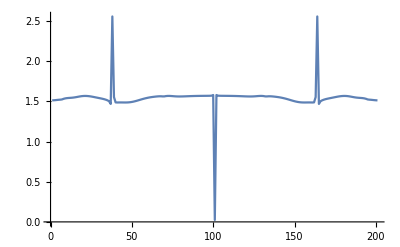

```mathematica
ListPlot[Table[ArcCos[Re[TEstates[[i]]*.(-Ldown[1, 64]-Lup[1, 64]).TEstates[[i]]]], {i, 1, Dimensions[TEstates][[1]]}], PlotRange->All, Joined->True]
```

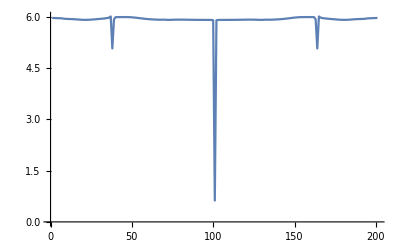

```mathematica
ListPlot[Mod[Re[Table[TEstates[[i]]*.(LzLz[1, 64]).TEstates[[i]], {i, 1, Dimensions[TEstates][[1]]}]], 2Pi], PlotRange->All, Joined->True]
```

```mathematica
HUbasis = Table[evecs[[i]]*.H.evecs[[j]], {i, 1, 129}, {j, 1, 129}];
init=Table[0, {i, 1, 129}];
init[[1]]=1;
TEUbstates = Table[MatrixExp[-I HUbasis t Pi].init, {t, -3, 3, 0.01}];
```

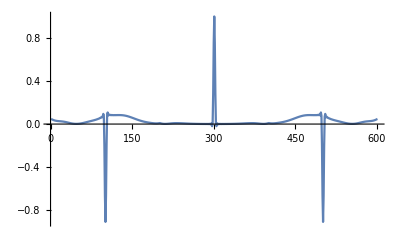

```mathematica
ListPlot[Table[TEUbstates[[i]]*.(-DiagonalMatrix[evals]).TEUbstates[[i]], {i, 1, Dimensions[TEUbstates][[1]]}], PlotRange->All, Joined->True]
```

```mathematica
ListPlot3D[Abs[TEUbstates]^2, PlotRange->All]
```

-Graphics3D-

```mathematica
{evals, evecs}=Eigensystem[Cldown[1, 64]+Clup[1, 64]//N];
evecs=(Normalize/@evecs[[Ordering[evals]]]);
```

```mathematica
Hcl = ClPlaqOperator[1,64]//N;
TEclstates=Table[MatrixExp[-I Hcl t].evecs[[1]], {t, -20, 20, 0.1}];
```

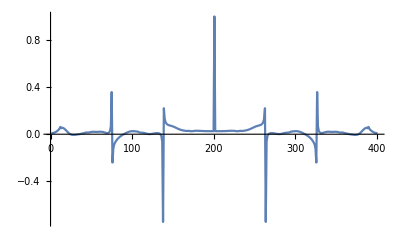

```mathematica
ListPlot[Table[TEclstates[[i]]*.(-Cldown[1, 64]-Clup[1, 64]).TEclstates[[i]], {i, 1, 401}], PlotRange->All, Joined->True]
```

```mathematica
|
```

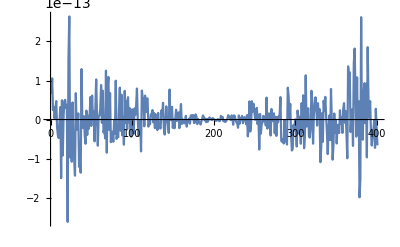

```mathematica
ListPlot[Table[TEclstates[[i]]*.(-Cldown[1, 64]+Clup[1, 64]).TEclstates[[i]]/I, {i, 1, 401}], PlotRange->All, Joined->True]
```

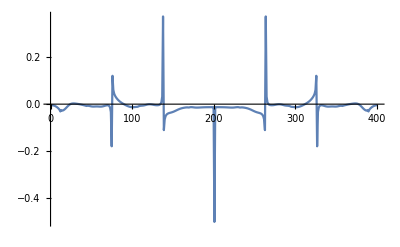

```mathematica
ListPlot[Table[TEclstates[[i]]*.Clup[1, 64].TEclstates[[i]], {i, 1, 401}], PlotRange->All, Joined->True]
```